Solving PDE on finite element mesh...

Oxide voltage share under the drain = 0.541 (Expected: > 0.5)

-Graphics3D-

-Graphics3D-

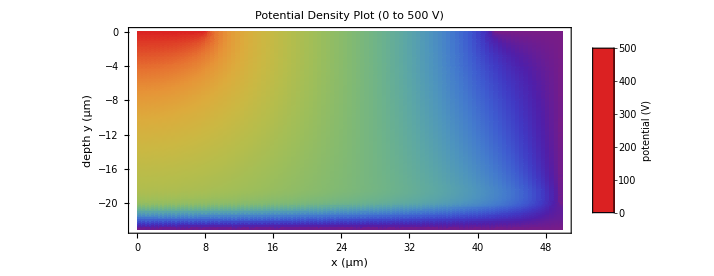

```mathematica
(* ============================================================================Nakagawa 1990 Fig.4-- STANDALONE 2-D Poisson solve+3-D plot Translated from Python Finite-Volume to Mathematica FEM============================================================================*)ClearAll["Global`*"];
Needs["NDSolve`FEM`"];

(*-----------------------------physical constants----------------------------*)
q=1.602176634*10^-19;      (*elementary charge,C*)
eps0=8.8541878128*10^-14;  (*vacuum permittivity,F/cm*)
KSi=11.7;                    (*relative permittivity,silicon*)
KOx=3.9;                     (*relative permittivity,SiO2*)
um=1.0*10^-4;              (*1 micron in cm*)

(*-----------------------------device parameters-----------------------------*)
Lsi=20.0*um;               (*silicon-film thickness*)
tox=3.0*um;                (*buried-oxide thickness*)
Lx=50.0*um;                (*lateral extent*)
wn=2.0*um;                 (*shallow donor-sheet thickness*)
ND0=1.0*10^14;             (*background donor density,cm^-3*)
SD=1.5*10^12;              (*shallow-sheet dose,cm^-2*)
drainw=8.0*um;             (*drain electrode width*)
sourcew=8.0*um;            (*source electrode width*)
H=Lsi+tox;                 (*total depth*)
Vapp=500.0;                  (*applied voltage*)

(* ============================================================================PDE ASSEMBLY& SOLVE============================================================================*)

(*---material permittivity and space charge---*)
eps[x_,y_]:=If[y<Lsi,KSi*eps0,KOx*eps0];
Ndon[x_,y_]:=If[y<Lsi,ND0+If[y>=Lsi-wn,SD/wn,0.0],0.0];
rho[x_,y_]:=q*Ndon[x,y];

(*---PDE---*)
(*Inactive[Div] and Inactive[Grad] strictly enforce displacement continuity (D_y) across the discontinuous Si/Oxide permittivity interface.*)
pde=Inactive[Div][-eps[x,y]*Inactive[Grad][phi[x,y],{x,y}],{x,y}]==rho[x,y];

(*---Dirichlet boundary conditions (structure B)---*)
bcBottom=DirichletCondition[phi[x,y]==0.0,y==H];
bcDrain=DirichletCondition[phi[x,y]==Vapp,y==0&&x<=drainw];
bcSource=DirichletCondition[phi[x,y]==0.0,y==0&&x>=Lx-sourcew];
bcSinker=DirichletCondition[phi[x,y]==0.0,x==Lx&&y<=Lsi];

bcs={bcBottom,bcDrain,bcSource,bcSinker};

(*---Mesh Generation& Solve---*)
(*Force mesh nodes onto the material and doping interfaces for precision*)
reg=Rectangle[{0,0},{Lx,H}];
mesh=ToElementMesh[reg,"IncludePoints"->Flatten[Table[{x,y},{x,0,Lx,Lx/10},{y,{Lsi-wn,Lsi}}],1],MaxCellMeasure->1.0*10^-8];

Print["Solving PDE on finite element mesh..."];
sol=NDSolveValue[{pde,bcs},phi,{x,y}∈mesh];

(* ============================================================================VERIFICATION============================================================================*)

drainMiddle=drainw/2.0;
vIf=sol[drainMiddle,Lsi];
oxideShare=vIf/Vapp;
siShare=1.0-oxideShare;

Print["Oxide voltage share under the drain = ",NumberForm[oxideShare,{4,3}]," (Expected: > 0.5)"];

(* ============================================================================3-D PLOT WITH LABELS& LEGENDS============================================================================*)

(*---Box styles for the callouts---*)
boxStyle={Background->Directive[White,Opacity[0.9]],FrameStyle->GrayLevel[0.5],RoundingRadius->3};

siBox=Framed[Style["Silicon film 0-20 μm\n(\[Approx]"<>ToString[Round[100*siShare]]<>"% of V)",10,Black,TextAlignment->Center],Evaluate@Sequence@@boxStyle];

oxBox=Framed[Style["Buried oxide 20-23 μm\n> half of V (\[Approx]"<>ToString[Round[100*oxideShare]]<>"%)",10,Magenta,TextAlignment->Center],Evaluate@Sequence@@boxStyle];

(*1. Main PDE surface plot*)

surfacePlot=Plot3D[sol[x*um,y*um],{x,0,Lx/um},{y,0,H/um},ColorFunction->Function[{x,y,z},ResourceFunction["TurboColor"][z/Vapp]],ColorFunctionScaling->False,PlotRange->{0,Vapp},AxesLabel->{"x (μm)","depth y (μm)","potential (V)"},ScalingFunctions->{Identity,"Reverse",Identity},Mesh->{45,60},MeshStyle->Directive[GrayLevel[0.1],Opacity[0.7],Thickness[0.001]],PlotPoints->100]

Legended[Plot3D[sol[x*um,y*um],{x,0,Lx/um},{y,0,H/um},ColorFunction->"TemperatureMap",ColorFunctionScaling->True,PlotRange->{0,Vapp},AxesLabel->{"x (μm)","depth y (μm)","potential (V)"},ScalingFunctions->{Identity,"Reverse",Identity},Mesh->{45,60},MeshStyle->Directive[GrayLevel[0.1],Opacity[0.7],Thickness[0.001]],PlotPoints->100,PlotLegends->None],BarLegend[{"TemperatureMap",{0,Vapp}},LegendLabel->"potential (V)"]]

(*2. Si/Oxide Interface line*)
interfaceLine=ParametricPlot3D[{x,Lsi/um,sol[x*um,Lsi]},{x,0,Lx/um},PlotStyle->Directive[RGBColor[0.86,0.08,0.24],Thickness[0.006]]];

(*3. Additional annotations (Lines and Text)*)
annotations=Graphics3D[{Magenta,Thickness[0.01],Line[{{0,Lsi/um,vIf},{0,H/um,0}}],Text[Style["n layer / drain  (500 V)",10,Bold,Darker[Red]],{1,0,Vapp+25},{-1,-1}],Text[Style["p+ layer / source  (0 V)",10,Bold,Darker[Blue]],{Lx/um,1,55},{1,-1}],Text[siBox,{6,9.0,360}],Text[oxBox,{3,21.5,150}]}];


(* ============================================================================2-D CONTOUR PLOT (Equipotential Lines)============================================================================*)(* ============================================================================2-D CONTOUR PLOT (Equipotential Lines)-CORRECTED COLOR DATA============================================================================*)contourPlot=ContourPlot[sol[x*um,y*um],{x,0,Lx/um},{y,0,H/um},(*Draw a contour line every 25 V*)Contours->Range[0,Vapp,25],(*FIX:Swapped "Turbo" for "Rainbow" which is universally supported*)ColorFunction->Function[{z},ColorData["Rainbow"][z/Vapp]],ColorFunctionScaling->False,PlotRange->{0,Vapp},FrameLabel->{"x (μm)","depth y (μm)"},PlotLabel->Style["Equipotential Lines (0 to 500 V)",Bold,12],(*Scale y-axis downward to match the 3D plot and physical depth*)ScalingFunctions->{Identity,"Reverse"},AspectRatio->Automatic,ContourStyle->Directive[Black,Opacity[0.4],Thickness[0.001]],PlotLegends->Placed[(*FIX:Swapped "Turbo" for "Rainbow" here as well*)BarLegend[{ColorData["Rainbow"],{0,Vapp}},LegendLabel->"potential (V)",LegendMarkerSize->280],Right],Epilog->{(*Overlay the Si/Oxide interface line in red*)Directive[RGBColor[0.86,0.08,0.24],Thickness[0.005]],Line[{{0,Lsi/um},{Lx/um,Lsi/um}}]},ImageSize->600];

(* ============================================================================2-D DENSITY PLOT (Potential Heatmap)============================================================================*)densityPlot=DensityPlot[sol[x*um,y*um],{x,0,Lx/um},{y,0,H/um},(*High resolution for a smooth gradient*)PlotPoints->100,(*Color mapping using "Rainbow"*)ColorFunction->Function[{z},ColorData["Rainbow"][z/Vapp]],ColorFunctionScaling->False,PlotRange->{0,Vapp},FrameLabel->{"x (μm)","depth y (μm)"},PlotLabel->Style["Potential Density Plot (0 to 500 V)",Bold,12],(*Scale y-axis downward to match the physical depth*)ScalingFunctions->{Identity,"Reverse"},AspectRatio->Automatic,PlotLegends->Placed[BarLegend[{ColorData["Rainbow"],{0,Vapp}},LegendLabel->"potential (V)",LegendMarkerSize->280],Right],Epilog->{(*Overlay the Si/Oxide interface line in red for reference*)Directive[RGBColor[0.86,0.08,0.24],Thickness[0.005]],Line[{{0,Lsi/um},{Lx/um,Lsi/um}}]},ImageSize->600]
```